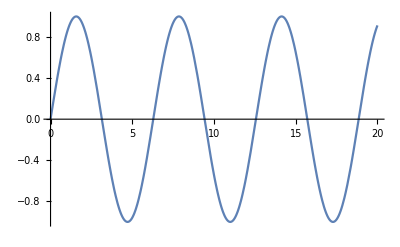
-Graphics-tyβ=0

./sin_graph.pdf

```mathematica
Labeled[Plot[Sin[t],{t,0,20}],Style[#,FontSize->20]&/@{t,y,"β=0"},{Bottom, Left,Top}]
Export["./sin_graph.pdf",%]
```

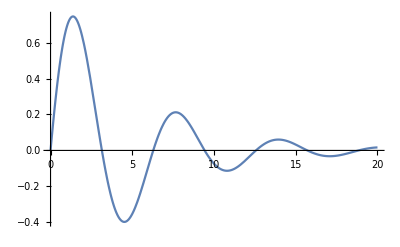
-Graphics-tyβ>0

./sin_exp_graph.pdf

```mathematica
Labeled[Plot[Exp[-t/5]*Sin[t],{t,0,20},PlotRange->All],Style[#,FontSize->20]&/@{t,y,"β>0"},{Bottom, Left,Top}]
Export["./sin_exp_graph.pdf",%]
```

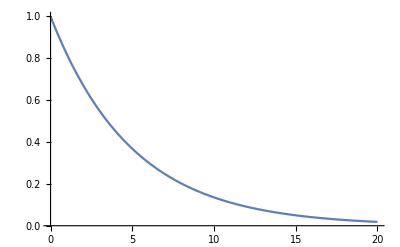
-Graphics-tyβ>>0

./exp_graph.pdf

```mathematica
Labeled[Plot[Exp[-t/5],{t,0,20},PlotRange->All],Style[#,FontSize->20]&/@{t,y,"β>>0"},{Bottom, Left, Top}]
Export["./exp_graph.pdf",%]
```